This is where Im conducting my a simulations for my Singular bee model as well as the Competitive model

First lets take a look at the simplistic Model

{ϕ→300,Ys→0.25,Us→250,hs→1,ms→0.1,r→0.05,Kd→1000,xreq→10000,δ→2,n0→30000,s0→1,d0→100}

{{n→InterpolatingFunction[…],s→InterpolatingFunction[…],d→InterpolatingFunction[…]}}

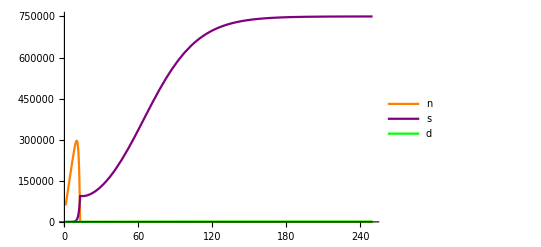

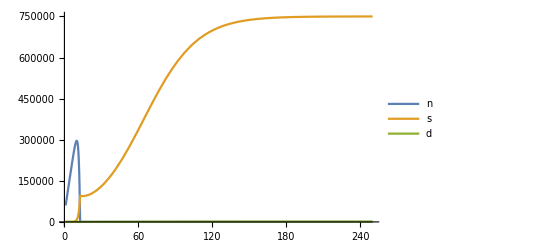

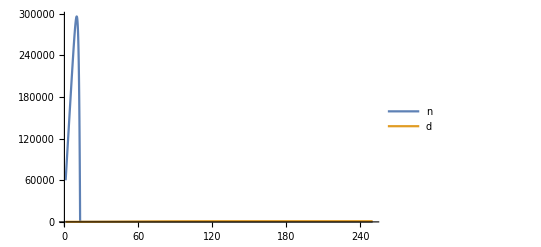

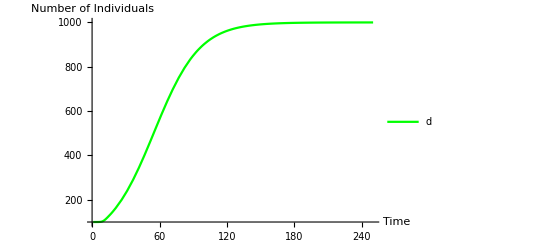

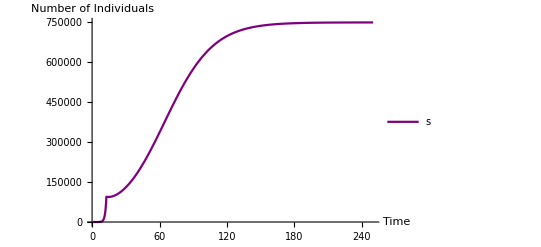

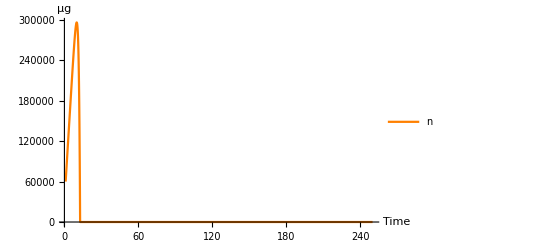

```mathematica
ClearAll["Global`*"]; 
pars = {ϕ -> 300, Ys -> .250, Us -> 250, hs ->1, ms -> 0.1, r -> 0.05, Kd -> 1000, xreq -> 10000, δ -> 2,n0 -> 30000, s0 ->1, d0 -> 100}
tmax = 250;

sim[pars_]:= NDSolve[
{n'[t] ==d[t]*ϕ - (1/Ys)*((Us*n[t]*s[t])/(1+Us*hs*n[t])),
s'[t] == (s[t]((Us*n[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == (r  (((s [t]δ )/xreq)/(1+(s[t] δ )/xreq)))*d[t]*(1-d[t]/Kd),
n[0]== n0,
s[0]==s0,
d[0]==d0}/. pars,
{n,s,d}, 
{t, 1, tmax}]
(*Set up the plot*)
sol = sim[pars]

Plot[{n[t]/.sol,s[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n, s,d}, PlotRange -> All, PlotStyle->{{Orange},{Purple}, {Green}}]
Plot[{n[t]/.sol,s[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n, s,d}, PlotRange -> All]
Plot[{n[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n,d}, PlotRange -> All]
Plot[{d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {d}, PlotRange -> All, PlotStyle->{{Green}}, AxesLabel->{"Time", "Number of Individuals"}]
Plot[{s[t]/.sol}, {t, 1, tmax}, PlotLegends -> {s}, PlotRange -> All, PlotStyle->{{Purple}}, AxesLabel->{"Time", "Number of Individuals"}]
Plot[{n[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n}, PlotRange -> All, PlotStyle->{{Orange}}, AxesLabel->{"Time", "μg"}]
```

Lets look at some more realistic Values for this Model.

{ϕ→85.714,Ys→0.1176,Us→1176000,hs→0.000167,ms→0.05,r→0.05,Kd→1000,xreq→100000,δ→2,n0→857.14,s0→1,d0→10}

{{n→InterpolatingFunction[…],s→InterpolatingFunction[…],d→InterpolatingFunction[…]}}

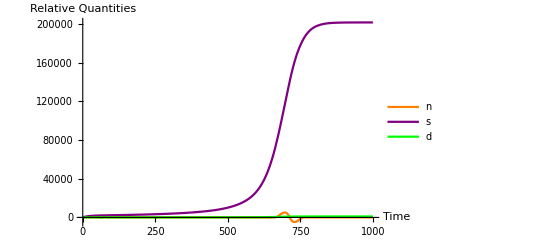

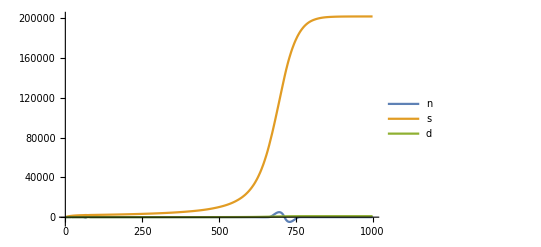

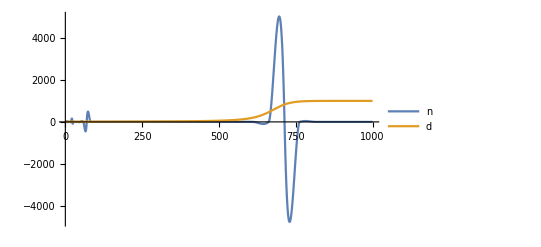

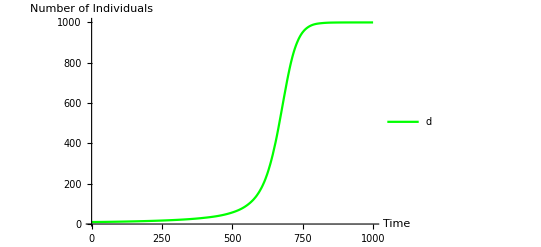

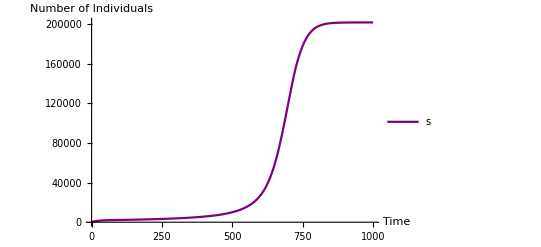

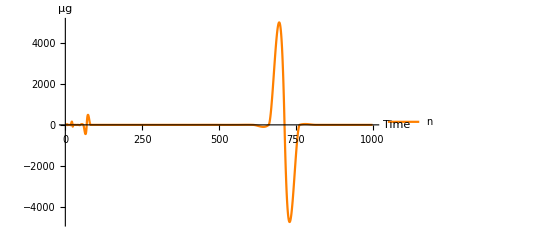

```mathematica
ClearAll["Global`*"]; 
pars = {ϕ -> 85.714, Ys -> 0.1176000, Us ->  1176000, hs ->0.000167, ms -> 0.05, r -> 0.05, Kd -> 1000, xreq -> 100000, δ -> 2,n0 -> 857.14, s0 ->1, d0 -> 10}
tmax = 1000;

sim[pars_]:= NDSolve[
{n'[t] ==d[t]*ϕ - (1/Ys)*((Us*n[t]*s[t])/(1+Us*hs*n[t])),
s'[t] == (s[t]((Us*n[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == (r  (((s [t]δ )/xreq)/(1+(s[t] δ )/xreq)))*d[t]*(1-d[t]/Kd),
n[0]== n0,
s[0]==s0,
d[0]==d0}/. pars,
{n,s,d}, 
{t, 1, tmax}, Method -> "StiffnessSwitching"]
(*Set up the plot*)
sol = sim[pars]

Plot[{n[t]/.sol,s[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n, s,d}, PlotRange -> All, PlotStyle->{{Orange},{Purple}, {Green}}, AxesLabel->{"Time", "Relative Quantities"}]
Plot[{n[t]/.sol,s[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n, s,d}, PlotRange -> All]
Plot[{n[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n,d}, PlotRange -> All]
Plot[{d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {d}, PlotRange -> All, PlotStyle->{{Green}}, AxesLabel->{"Time", "Number of Individuals"}]
Plot[{s[t]/.sol}, {t, 1, tmax}, PlotLegends -> {s}, PlotRange -> All, PlotStyle->{{Purple}}, AxesLabel->{"Time", "Number of Individuals"}]
Plot[{n[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n}, PlotRange -> All, PlotStyle->{{Orange}}, AxesLabel->{"Time", "μg"}]
```

```mathematica
(*Seems that Chaotic things occur when we simulate this simplistic model using the literature's estimates. Probably dealing with one of those positive eigen values...*)
```

Lets preform some simulations using the competition model. Lets use literature values here since we have them.

{{n→InterpolatingFunction[…],s→InterpolatingFunction[…],d→InterpolatingFunction[…],a→InterpolatingFunction[…],e→InterpolatingFunction[…],g→InterpolatingFunction[…]}}

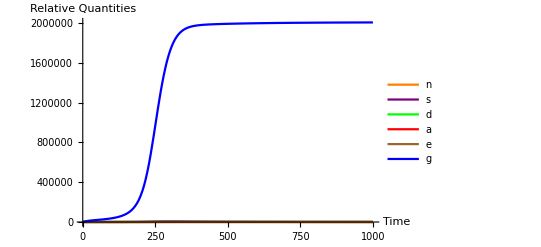

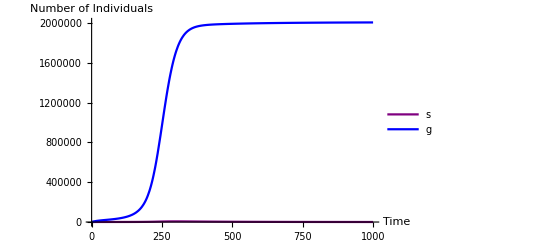

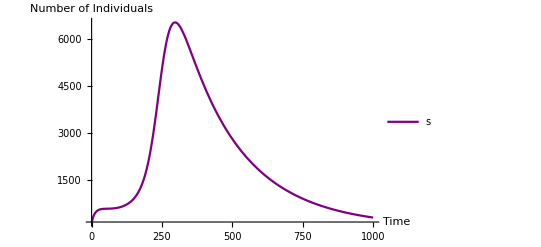

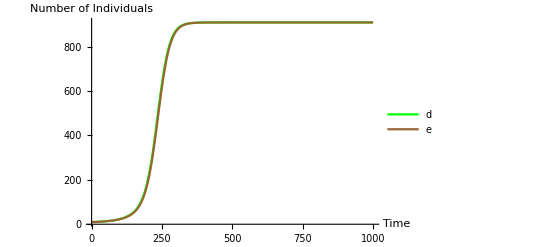

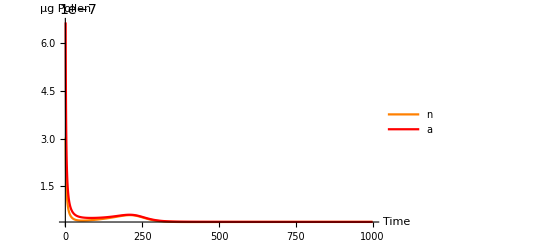

```mathematica
ClearAll["Global`*"]; 
Clear[ϕ, Ys, Us, hs, ms, r, Kd, Ke, Yg, Ug, hg, mg, β, α, xreq, n0, s0, d0, g0, e0, a0]; 
pars2 = {ϕ -> 85.714, Ys -> 0.1176000, Us -> 1176000, hs -> 0.000167, ms -> 0.05, r->0.05, Kd -> 1000,Ke -> 1000, Yg -> 0.64448, Ug -> 644448, hg ->0.000304, mg ->0.05, β ->0.1, α -> 0.1,xreq -> 100000,  n0 -> 857.14, s0 -> 1, d0 -> 10, g0 -> 1, e0 -> 10, a0 -> 857.14,δ->2};
tmax2= 1000;

sim2 [pars2_]:=NDSolve[
{n'[t]==d[t]ϕ - (1/Ys)((Us*n[t]*s[t])/(1+Us*hs*n[t])) - (1/Yg)((Ug * n[t] g[t])/(1 + Ug hg n[t] + Ug hg a[t])),
a'[t] == e[t]ϕ - (1/Yg)((Ug *a[t] g[t])/(1 + Ug hg n[t]+ Ug hg a[t])),
g'[t] == (g[t] (Ug a[t]+ Ug n[t])/(1 + Ug hg n[t] + Ug hg a[t])) - mg *g[t], 
s'[t] == (s[t]((Us*n[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == (r  (((s[t]  δ + g[t])/xreq)/(1+(s[t]δ + g[t])/xreq)))d[t](Kd - d[t] - β e[t])/Kd,
e'[t] == (r  ((( g[t])/xreq)/(1 + ( g[t])/xreq))) e[t](Ke - e[t] - α d[t])/Ke,
n[0 ]== n0, 
s[0]==s0,
d[0]==d0,
a[0]==a0,
e[0]==e0,
g[0]==g0}/.pars2,
{n,s,d, a, e, g}, 
{t, 1, tmax2}(*,
Method -> "StiffnessSwitching"*)]
sol2 = sim2[pars2]
Plot[{n[t]/.sol2, s[t]/.sol2, d[t] /. sol2,  a[t] /. sol2, e[t] /. sol2 ,  g[t] /. sol2},{t,1,tmax2}, PlotLegends -> {n,s,d,a,e,g}, PlotRange -> All, PlotStyle -> {{Orange}, {Purple}, {Green}, {Red}, {Brown}, {Blue}}, AxesLabel->{"Time", "Relative Quantities"}] 
Plot[{s[t]/.sol2, g[t] /. sol2},{t,1,tmax2}, PlotLegends -> {s,g}, PlotRange -> All, PlotStyle->{{Purple}, {Blue}}, AxesLabel->{"Time", "Number of Individuals"}] 
Plot[{s[t]/.sol2},{t,1,tmax2}, PlotLegends -> {s}, PlotRange -> All, PlotStyle -> {{Purple}}, AxesLabel->{"Time", "Number of Individuals"}] 
Plot[{ d[t] /. sol2,  e[t] /. sol2 },{t,1,tmax2}, PlotLegends -> {d,e}, PlotRange -> All, PlotStyle -> {{Green}, {Brown}}, AxesLabel->{"Time", "Number of Individuals"}] 
Plot[{n[t]/.sol2, a[t] /. sol2},{t,1,tmax2}, PlotLegends -> {n,a}, PlotRange -> All, PlotStyle -> {{Orange}, {Red}}, AxesLabel->{"Time", "μg Pollen"}]
```

```mathematica
(*Seems that specialist bees are driven to extinction at their stable state. Its interesting that they do persist in the system while pollen/plants are increasing however*)
```

What if Native Plants are Competitively Dominant as according to our bifurcation diagrams?

{{n→InterpolatingFunction[…],s→InterpolatingFunction[…],d→InterpolatingFunction[…],a→InterpolatingFunction[…],e→InterpolatingFunction[…],g→InterpolatingFunction[…]}}

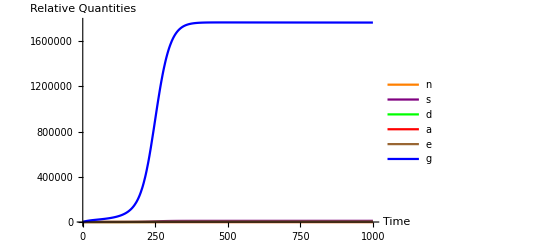

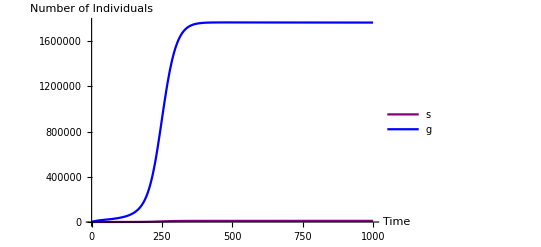

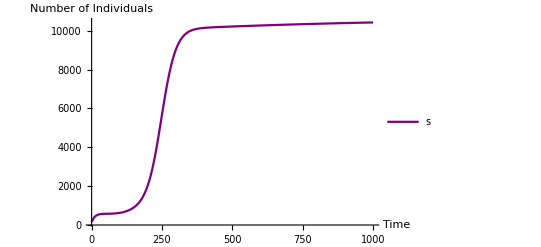

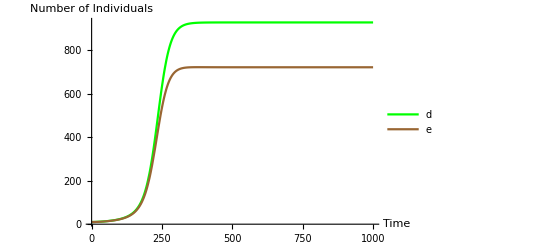

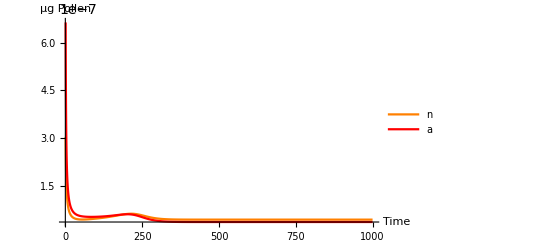

```mathematica
ClearAll["Global`*"]; 
Clear[ϕ, Ys, Us, hs, ms, r, Kd, Ke, Yg, Ug, hg, mg, β, α, xreq, n0, s0, d0, g0, e0, a0]; 
pars2 = {ϕ -> 85.714, Ys -> 0.1176000, Us -> 1176000, hs -> 0.000167, ms -> 0.05, r->0.05, Kd -> 1000,Ke -> 1000, Yg -> 0.64448, Ug -> 644448, hg ->0.000304, mg ->0.05, β ->0.1, α -> 0.3,xreq -> 100000,  n0 -> 857.14, s0 -> 1, d0 -> 10, g0 -> 1, e0 -> 10, a0 -> 857.14,δ->2};
tmax2= 1000;

sim2 [pars2_]:=NDSolve[
{n'[t]==d[t]ϕ - (1/Ys)((Us*n[t]*s[t])/(1+Us*hs*n[t])) - (1/Yg)((Ug * n[t] g[t])/(1 + Ug hg n[t] + Ug hg a[t])),
a'[t] == e[t]ϕ - (1/Yg)((Ug *a[t] g[t])/(1 + Ug hg n[t]+ Ug hg a[t])),
g'[t] == (g[t] (Ug a[t]+ Ug n[t])/(1 + Ug hg n[t] + Ug hg a[t])) - mg *g[t], 
s'[t] == (s[t]((Us*n[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == (r  (((s[t]  δ + g[t])/xreq)/(1+(s[t]δ + g[t])/xreq)))d[t](Kd - d[t] - β e[t])/Kd,
e'[t] == (r  ((( g[t])/xreq)/(1 + ( g[t])/xreq))) e[t](Ke - e[t] - α d[t])/Ke,
n[0 ]== n0, 
s[0]==s0,
d[0]==d0,
a[0]==a0,
e[0]==e0,
g[0]==g0}/.pars2,
{n,s,d, a, e, g}, 
{t, 1, tmax2}(*,
Method -> "StiffnessSwitching"*)]
sol2 = sim2[pars2]
Plot[{n[t]/.sol2, s[t]/.sol2, d[t] /. sol2,  a[t] /. sol2, e[t] /. sol2 ,  g[t] /. sol2},{t,1,tmax2}, PlotLegends -> {n,s,d,a,e,g}, PlotRange -> All, PlotStyle -> {{Orange}, {Purple}, {Green}, {Red}, {Brown}, {Blue}}, AxesLabel->{"Time", "Relative Quantities"}] 
Plot[{s[t]/.sol2, g[t] /. sol2},{t,1,tmax2}, PlotLegends -> {s,g}, PlotRange -> All, PlotStyle->{{Purple}, {Blue}}, AxesLabel->{"Time", "Number of Individuals"}] 
Plot[{s[t]/.sol2},{t,1,tmax2}, PlotLegends -> {s}, PlotRange -> All, PlotStyle -> {{Purple}}, AxesLabel->{"Time", "Number of Individuals"}] 
Plot[{ d[t] /. sol2,  e[t] /. sol2 },{t,1,tmax2}, PlotLegends -> {d,e}, PlotRange -> All, PlotStyle -> {{Green}, {Brown}}, AxesLabel->{"Time", "Number of Individuals"}] 
Plot[{n[t]/.sol2, a[t] /. sol2},{t,1,tmax2}, PlotLegends -> {n,a}, PlotRange -> All, PlotStyle -> {{Orange}, {Red}}, AxesLabel->{"Time", "μg Pollen"}]
```

```mathematica
(*Now the specialist is capable of staying in the system a stable equilibrium over long term dynamics. Would be interesting to use this idea in an invasion analysis?*)
```